```mathematica
f1[x_] = (2 (1+ x^{-1}) Log[1+x] - 2);
f2[x_] = -2 x^{-1} (Sqrt[1-x^2] ArcCos[x] -Pi/2)-2;
```

```mathematica
Series[f1[c x] x^{-1},{x,0,10}]
Series[f2[c x] x^{-1}, {x,0,10}]
```

{c-(c^2 x)/3+(c^3 x^2)/6-(c^4 x^3)/10+(c^5 x^4)/15-(c^6 x^5)/21+(c^7 x^6)/28-(c^8 x^7)/36+(c^9 x^8)/45-(c^10 x^9)/55+(c^11 x^10)/66+O[x]^11}

{(c π)/2-(2 c^2 x)/3+1/8 c^3 π x^2-(4 c^4 x^3)/15+1/16 c^5 π x^4-(16 c^6 x^5)/105+5/128 c^7 π x^6-(32 c^8 x^7)/315+7/256 c^9 π x^8-(256 c^10 x^9)/3465+(21 c^11 π x^10)/1024+O[x]^11}

```mathematica
Series[(f2[c x] -f1[c x]) x^{-1},{x,0,10}]
```

{1/2 c (-2+π)-(c^2 x)/3+1/24 c^3 (-4+3 π) x^2-(c^4 x^3)/6+(-c^5/15+(c^5 π)/16) x^4-(11 c^6 x^5)/105+(-c^7/28+(5 c^7 π)/128) x^6-(31 c^8 x^7)/420+(-c^9/45+(7 c^9 π)/256) x^8-(193 c^10 x^9)/3465+(-c^11/66+(21 c^11 π)/1024) x^10+O[x]^11}

```mathematica
Limit[(f2[x]-f1[x])^{-1}  x, x->0]
Limit[(f1[x])^{-1}  x, x->0]
Limit[(f2[x])^{-1}  x, x->0]
```

{2/(-2+π)}

{1}

{2/π}

```mathematica
{1}
```

{1}

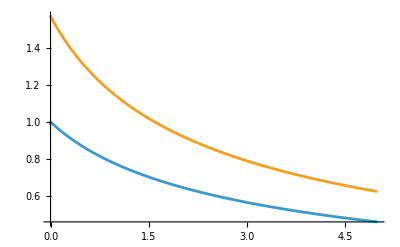

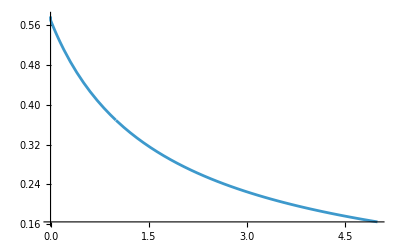

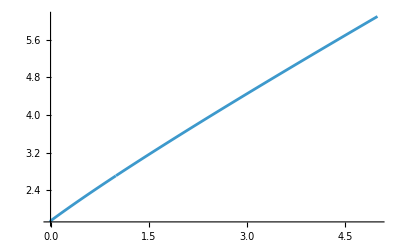

```mathematica
Plot[ {f1[x] x^{-1} , f2[x] x^{-1}}, {x, 0,5}]
Plot[ (f2[x]-f1[x])  x^{-1}, {x, 0,5}]
Plot[ (f2[x]-f1[x])^{-1}  x, {x, 0,5}]
```

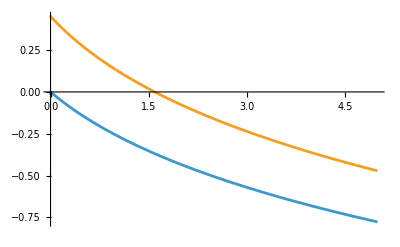

```mathematica
Plot[{Log[f1[x] x^{-1} ], Log[f2[x] x^{-1}]}, {x, 0,5}]
```

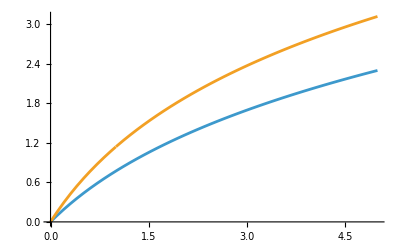

```mathematica
Plot[ {f1[x]  , f2[x]}, {x, 0,5}]
```

```mathematica
Manipulate[Plot[ {(f2[x]-f1[x])^{-1}  x, 2/(-2+π)+b * x+c*x^2},{x,0,10}],{b,0,4},{c,-0.01, 0}]
```

```mathematica
Manipulate[Plot[ {(f2[x]-f1[x])^{-1}  x/( 2/(-2+π)+b * x),1 -c x^2},{x,0,10}, PlotPoints->1000],{{b, 0.868133} ,0.8,1.2},{{c,0},0., 0.1}]
```

```mathematica
b = 0.868133
```

0.868133

```mathematica
Manipulate[Plot[ {1./(1+b*x), (f1[x])x^{-1}},{x,0,10}, PlotPoints->1000],{{b, 1} ,0.,1.},{{c,0},0., 0.1}]
```

```mathematica
Manipulate[Plot[ {( 1+b*x)/(1+c x) (f1[x])x^{-1}, 1.015, 0.985},{x,0,10}, PlotPoints->1000],{{b,0.34} ,0.3,0.37},{{c,0.046},0.04, 0.05}]
```

```mathematica
b=0.34;
c= 0.046
```

0.046

```mathematica
(*1.5% accuracy for f1[x] for x \in[0,10] *)
```

```mathematica
b = 0.34
c = 0.046
```

0.34

0.046

```mathematica
Manipulate[Plot[ {(1+c x)/( 1+b*x), (f1[x])x^{-1}},{x,0,10}, PlotPoints->1000],{{b,0.34} ,0.3,0.37},{{c,0.046},0.04, 0.05}]
```